## Numerical results for trophical transmission model with multiple infections

```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - η Is ;
dIwdt =  (1-p)η Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p η Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 

dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + (1-q)λww) Ds- (μ + σw) Dw - ((1-q)λww +λw)Dw;
dDwwdt =  q λww Ds + ((1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - η Is;

forceInf = {η -> γ W, λw ->h(ρ +  βw) Iw, λww ->h(ρ + βww) Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

```mathematica
dDsdt + dDwdt + dDwwdt//FullSimplify
```

-Ds μ-Dw (μ+σw)-Dww (μ+σww)+B[Ds,Dw,Dww,Is,Iw,Iww]

# Reproduction ratio R0

```mathematica
R0 = γ Is(p q h(βww + ρ))/(αww+d+ Πww[Ds, Dw, Dww,βww])  Ds/(μ+σww) fww/(δ+γ Is) +
γ Is (((1-p)(βw + ρ)h)/(αw+d+ Πw[Ds, Dw,Dww, βw]) + (p (1-q)(βww + ρ)h)/(αww+d+ Πww[Ds, Dw, Dww,βww]))  Ds/(μ+ σw)fw/(δ+γ Is);
```

# Graph format and parallel computation

```mathematica
includeFrame = True(*{{True, False}, {True,False}}*);
imageSize = 600;
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 24};
colorlist = ColorData[97,"ColorList"]
colorstable = ColorData[97,"ColorList"][[{1, 2, -2}]]
ihostCol = ColorData[97,"ColorList"][[1]];
 dhostCol = ColorData[97,"ColorList"][[4]];
fCol1 = ColorData[97,"ColorList"][[3]];
fCol2 = ColorData[97,"ColorList"][[-1]];
pointsize = 0.02;
figResolution = 300;
colbifur = {Black, Black, Black, Black}(*{Black, Darker[Gray], Gray, Lighter[Gray]}*)
colbifurfilling = {Lighter[Gray, 0.1],Lighter[Gray, 0.3], Lighter[Gray, 0.5], Lighter[Gray, 0.7]}
panellabel = 250;
thick = 0.003;
coldat = "Pastel";
intorder = 5;
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.736782672705901, 0.358, 0.5030266573755369]}

{GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0]}

{RGBColor[0.55, 0.55, 0.55],RGBColor[0.65, 0.65, 0.65],RGBColor[0.75, 0.75, 0.75],RGBColor[0.85, 0.85, 0.85]}

# Linear birth function for intermediate host

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, t,sysfunc0];
solsds = Solve[Thread[sysfunc0 == 0]/.{Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0, W-> 0}, varRes][[2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{Is→μ/(c ρ),Ds→-(d-r)/ρ}

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories

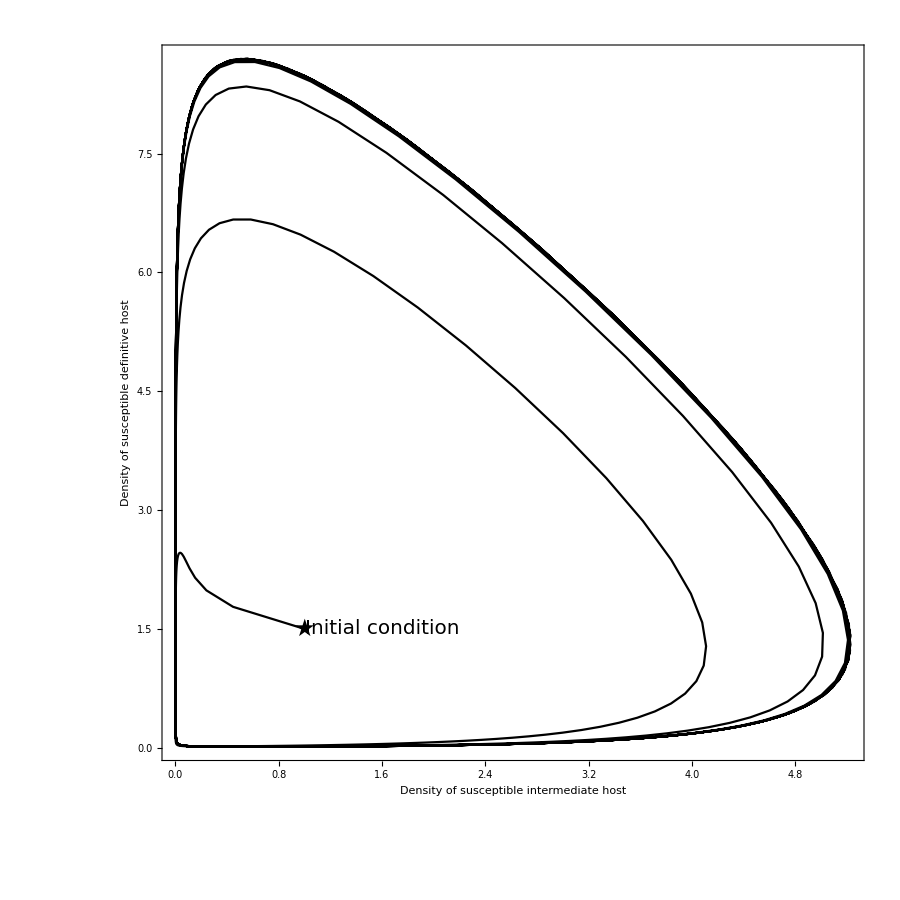

diseasefree_linear.pdf

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9, h-> 0.8};

maxt = 100;

init0= {Is[0]== 1, Iw[0] == 1,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

range = {{-1, 20},{-1, 20}};

epilogParasite01 = { {Black, Line[{{8.5, 0.03}, {10.1, 0.81}}]},{Black, Line[{{7.5, 0.23}, {5.1, 0.81}}]}, {ihostCol, Text[Style["Doubly Infected \n Intermediate Host", FontSize->14], {10., 1.}, {-0.8, 0}]},{ihostCol, Text[Style["Singly Infected \n Intermediate Host", FontSize->14], {4., 1.}, {-0.8, 0}]}};
epilogParasite02= {{Black, Line[{{10.5, 0.03}, {11.5, 0.75}}]}, {Black, Line[{{8.5, 0.3}, {5.1, 0.8}}]},{dhostCol, Text[Style["Doubly Infected \n Definitive Host", FontSize->14], {10.9, 0.9}, {-0.8, 0}]}, {dhostCol, Text[Style["Singly Infected \n Definitive Host", FontSize->14], {4., 1.}, {-0.8, 0}]}};
epilogParasite03 =  {{Black, Line[{{9.5, 9.03}, {8.5, 0.98}}]}, {Black, Text[Style["Freeliving Parasites", FontSize->14], {9., 10.}, {-0.8, 0}]}};

p11 = Plot[Evaluate[{Iw[t], Iww[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 20}, All}, AspectRatio-> 1/3, ImageSize->imageSize/3, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->{{ihostCol, Dashed,Thickness[0.005]}, {ihostCol, DotDashed,Thickness[0.005]}}, Epilog->epilogParasite01];
p12= Plot[Evaluate[{ Dw[t], Dww[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 20}, All},AspectRatio-> 1/3,ImageSize->imageSize/3, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->{{dhostCol, Dashed,Thickness[0.005]}, {dhostCol, DotDashed,Thickness[0.005]}}, Epilog->epilogParasite02];
p13 = Plot[Evaluate[{W[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 20}, All},AspectRatio-> 1/3, ImageSize->imageSize/3, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->{Gray, Thickness[0.005]}, Epilog->epilogParasite03];
p1 =GraphicsColumn[{p11, p12, p13}, Spacings->0, ImageSize->{900, 1000},Epilog->{Text[Style["Time", Black, 24],{Center,-215}],Rotate[Text[Style["Host Density", Black, 24],{0.5,Center}],90 Degree]}];


epilogHost0 = {{Black, Text[Style[★, FontSize->24], {1., 1.5}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->20], {1., 1.5}, {-1.3, -0.2}]}};
p2 = ParametricPlot[{Evaluate[{Is[t], Ds[t]}/.ndsol0]}, {t, 0, maxt}, AspectRatio->1, PlotRange->All, Frame->includeFrame, PlotStyle->Black, FrameStyle->frameStyle, FrameLabel->{Style["Density of \n susceptible intermediate host",Black,24], Style["Density of \n susceptible definitive host",Black,24]}, ImageSize->imageSize * 1.5, LabelStyle->labelStyle, Epilog->epilogHost0];

GraphicsRow[{p1, p2}, ImageSize->{1500, 1000}, Spacings->0, Epilog->{Text[Style["A)", Black, 24], {100, -10}], Text[Style["B)", Black, 24], {900, -10}]}]
(*Export["diseasefree_linear.pdf",%, ImageResolution-> figResolution]*)
```

# Nonlinear birth function for intermediate host

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  (ρ +βw)(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  (ρ+βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, t, sysfunc1];
Thread[sysfunc1==0]/.{Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0, W-> 0};
diseasefree = Solve[%, {Is, Ds}][[3]];

R0func1 = R0/.func1/.Dw -> 0/.Dww-> 0/.Iw-> 0/.Iww-> 0//Simplify;
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories

## Disease free equilibrium

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26, h-> 0.8};

maxt = 100;

solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];
range1 = { {-0.05, 2.4}, {-0.05, 0.7}};
{Is[0]== 1.2, Iw[0] == 0.2,Iww[0]==0.3, Ds[0] ==0.5, Dw[0] == 0.7,Dww[0]==0.1, W[0] == 0.8};
ndsolNL = NDSolve[Join[sysNDSolvefunc1/.prEcoNL, %], varRes, {t, 0, maxt}] ;

ieq1 = Evaluate[Is[maxt]/.ndsolNL][[1]];
deq1 = Evaluate[Ds[maxt]/.ndsolNL][[1]];

epilogHost1 = {{Black, PointSize[pointsize],Point[{{ieq1, deq1}}]}, {Black, Text[Style[★, FontSize->24], {1.2, 0.5}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->14], {1.2, 0.5}, {-1.2, -0.2}]}, {Black, Text[Style["Equilibrium", FontSize->14], {ieq1, deq1}, {1.2, -0.2}]}};
ppHost1 = ParametricPlot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, AspectRatio->1, Frame->includeFrame, PlotStyle->Black, FrameStyle -> frameStyle, PlotRange->range1, FrameLabel->{"Density of \n Susceptible Intermediate Host", "Density of \n Susceptible Definitive Host"}, LabelStyle->labelStyle,   ImageSize->imageSize/1.1, Epilog->epilogHost1];

epilogParas11 = { {ihostCol, Text[Style["Singly Infected \n Intermediate Hosts", FontSize->14], {2, 0.6}, {-1.05, 0}]}, {ihostCol, Text[Style["Doubly Infected \n Intermediate Hosts", FontSize->14], {7, 0.2}, {-1.05, 0}]}};
epilogParas12 = {{dhostCol, Text[Style["Doubly Infected \n Definitive Hosts", FontSize->14], {7, 0.2}, {-1.05, 0}]}, {dhostCol, Text[Style["Singly Infected \n Definitive Hosts", FontSize->14], {0.2, 0.6}, {-1.05, 0}]}};
epilogParas13 = {{Black, Text[Style["Freeliving Parasites", FontSize->14], {0.75, 0.8}, {-1.05, 0}]}};

ppParasite11 = Plot[Evaluate[{Iw[t], Iww[t]}/.ndsolNL], {t, 0, maxt}, AspectRatio->1/3,PlotRange->{{0, 10}, {-0.1, 1.2}}, PlotStyle->{{ihostCol, Dashed}, {ihostCol, DotDashed}}, Frame->includeFrame, ImageSize->imageSize, FrameStyle->frameStyle,Epilog->epilogParas11];
ppParasite12 = Plot[Evaluate[{ Dw[t], Dww[t]}/.ndsolNL], {t, 0, maxt}, AspectRatio->1/3,PlotRange->{{0, 10}, {-0.1, 1.2}}, PlotStyle->{{dhostCol, Dashed}, {dhostCol, DotDashed}},Frame->includeFrame,  ImageSize->imageSize, FrameStyle->frameStyle, Epilog->epilogParas12];
ppParasite13 = Plot[Evaluate[{W[t]}/.ndsolNL], {t, 0, maxt}, AspectRatio->1/3,PlotRange->{{0, 10}, {-0.1, 1.2}}, PlotStyle->Gray, Frame->includeFrame, ImageSize->imageSize, FrameStyle->frameStyle, Epilog->epilogParas13];ppParasite1 = GraphicsColumn[{ppParasite11, ppParasite12, ppParasite13}, Spacings->0, ImageSize->{600, 600}];
```

## Disease stable equilibrium

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.05, fw -> 45, fww-> 45,δ-> 0.9, k -> 0.26, h-> 0.6};

condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};

maxt =80;

range2 = {{-0.05, 2.3}, {-0.01, 0.12}};
init = {Is[0]==0.4588921303535818,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==0.4460456255182149,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472};
ndsolDS = NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, init], varRes, {t, 0, maxt}] ;

ieq2 = Evaluate[Is[maxt]/.ndsolDS][[1]];
deq2 = Evaluate[Ds[maxt]/.ndsolDS][[1]];
epilogHost2 = {{Black, PointSize[pointsize],Point[{{ieq2, deq2}}]}, {Black, Text[Style[★, FontSize->24], {0.4588921303535818,0.4460456255182149}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->14], {0.4588921303535818, 0.4460456255182149}, {-1.2, -0.2}]}, {Black, Text[Style["Equilibrium", FontSize->14], {ieq2, deq2}, {1.2, -0.2}]}};
ppHost2 = ParametricPlot[Evaluate[{Is[t], Ds[t]}/.ndsolDS], {t, 0, maxt},  Frame->includeFrame,AspectRatio->1, PlotStyle->Black, FrameStyle -> frameStyle, PlotRange->All, FrameLabel->{"Density of \n Susceptible Intermediate Host", "Density of \n Susceptible Definitive Host"}, LabelStyle->labelStyle, ImageSize->imageSize/1.1 , Epilog->epilogHost2];

epilogParas21 = {{ihostCol, Text[Style["Singly Infected \n Intermediate Hosts", FontSize->14], {30, -1.}, {-1.05, 0}]}, {ihostCol, Text[Style["Doubly Infected \n Intermediate Hosts", FontSize->14], {30, -4.2}, {-1.05, 0}]}};
epilogParas22 = {{dhostCol, Text[Style["Singly Infected \n Definitive Hosts", FontSize->14], {30, -4.1}, {-1.05, 0}]},{dhostCol, Text[Style["Doubly Infected \n Definitive Hosts", FontSize->14], {30, -7.5}, {-1.05, 0}]}};
epilogParas23 = {{Black, Text[Style["Freeliving Parasites", FontSize->14], {30, -3.2}, {-1.08, 0}]}};

trajectStyle = {{Gray, Thick}};

ppParasite21 =LogPlot[Evaluate[{Iw[t], Iww[t]}/.ndsolDS], {t, 0, maxt}, AspectRatio->1/3, PlotStyle->{{ihostCol, Dashed}, {ihostCol, DotDashed}},PlotRange-> All, Frame-> includeFrame, FrameStyle->frameStyle, ImageSize->imageSize, Epilog->epilogParas21] ;
ppParasite22 =LogPlot[Evaluate[{Dw[t], Dww[t]}/.ndsolDS], {t, 0, maxt}, AspectRatio->1/3, PlotStyle->{{dhostCol, Dashed}, {dhostCol, DotDashed}},PlotRange-> All, Frame-> includeFrame, FrameStyle->frameStyle,  ImageSize->imageSize, Epilog->epilogParas22] ;
ppParasite23 =LogPlot[Evaluate[{ W[t]}/.ndsolDS], {t, 0, maxt}, AspectRatio->1/3, PlotStyle->trajectStyle,PlotRange-> All, Frame-> includeFrame, FrameStyle->frameStyle, ImageSize->imageSize, Epilog->epilogParas23] ;


ppParasite2 = GraphicsColumn[{ppParasite21, ppParasite22, ppParasite23}, Spacings-> 0, ImageSize->{600, 600}];
```

## Combined disease free and disease stable ecology plot

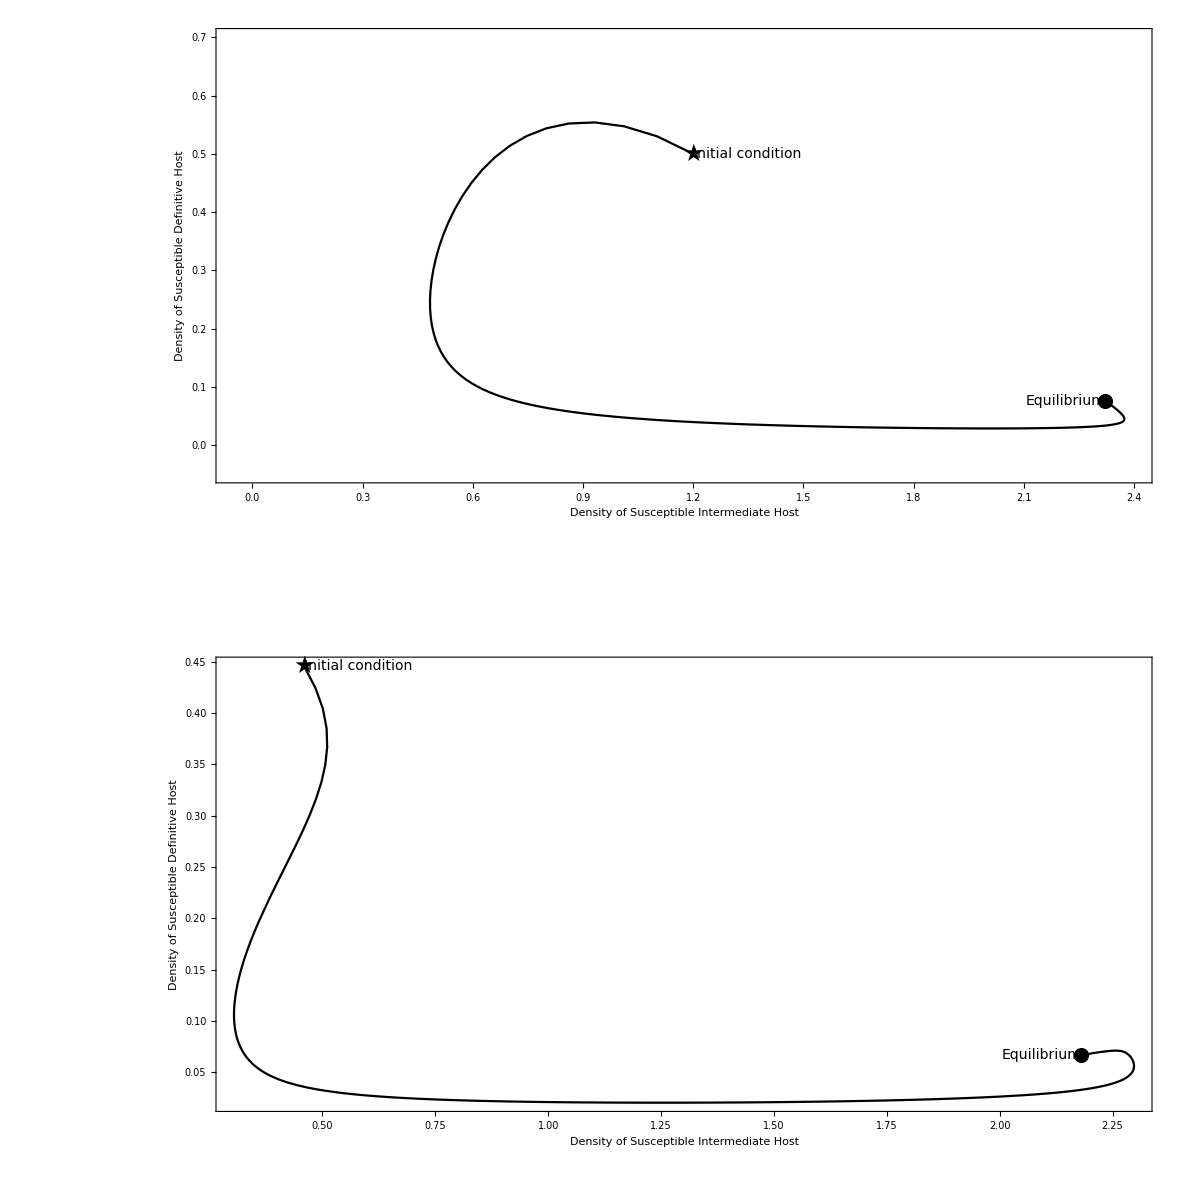

ecotraject_nonlinear.pdf

```mathematica
epilogAxesCombiPanel = {Text[Style["A)", Black, 24], {100, -10}], Text[Style["Time", Black, 24], {330, -520}],Rotate[Text[Style["Density", Black, 24], {100, -240}], 90 Degree], Text[Style["B)", Black, 24], {660, -10}],Text[Style["C)", Black, 24], {100, -590}], Text[Style["Time", Black, 24], {330, -1120}], Rotate[Text[Style["Density", Black, 24], {100, -840}], 90 Degree],  Text[Style["D)", Black, 24], {660, -590}]};
GraphicsGrid[{{ppParasite1, ppHost1}, {ppParasite2, ppHost2}}, ImageSize->{1200, 1200}, Spacings->0, Epilog->epilogAxesCombiPanel]
(*Export["ecotraject_nonlinear.pdf", %, ImageResolution-> figResolution]*)
```

## Bifurcation f_w (f_ww = ϵ f_w)

```mathematica
fwstart = 33;
fwend = 45;
fwstep = 0.1;
fwrange = Range[fwstart, fwend, fwstep];
```

## Parameter set 1 (bistability)

CALCULATE BIFURCATION

```mathematica
parfw1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4, h-> 0.6};
(*Find all solutions of the system with the given parameter values*)
solsfwAll1 = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw1/.fw-> 36) == 0], varRes, Reals];

(*Select disease circulation solutions*)
fwAllPositive1= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw1, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
(*Select disease free solutions*)
solsfwzero1 = Select[solsfwAll1, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];
```

CALCULATE DYNAMICS

```mathematica
maxt1 = 300;
init1 = {Is[0]==0.1588921303535818,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==0.4460456255182149,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472};
solsbistable1 = NDSolve[Join[sysNDSolvefunc1/.fww -> ϵ fw /.parfw1/.fw-> 39/.ϵ -> 4, init1], varRes, {t, 0, maxt1}] ;
maxt2 = 300;
init2 = {Is[0]==1.1588921303535818,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==0.4460456255182149,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472};
solsbistable2 = NDSolve[Join[sysNDSolvefunc1/.fww -> ϵ fw /.parfw1/.fw-> 39/.ϵ -> 4, init2], varRes, {t, 0, maxt2}] ;
```

PLOT

RGBColor[0.701961, 0.890196, 0.933333]

RGBColor[0.501961, 0.709804, 0.835294]

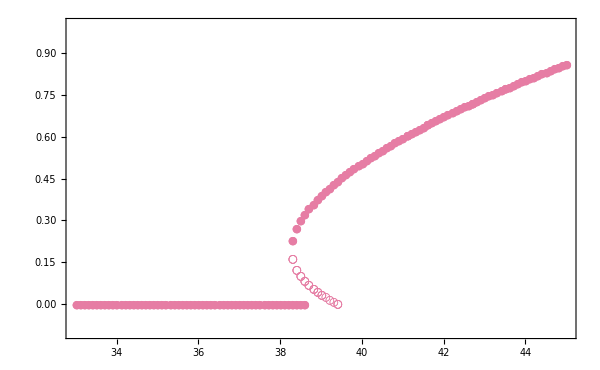

reproduction_bifurcationB.pdf

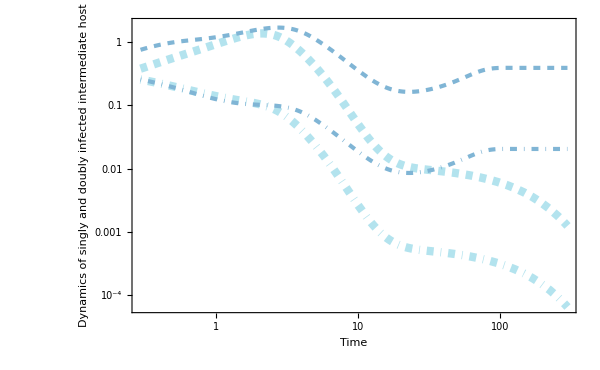

reproduction_bifurcationD.pdf

```mathematica
fwlist = fw/.Flatten[fwAllPositive1, 1];
eqfwlist = eq/.Flatten[fwAllPositive1, 1];
eqfwzero = ConstantArray[solsfwzero1, Length[fwrange]];
col1 = ColorData["GeologicAges", "ColorList"][[45]];
colLine1 = ColorData["GeologicAges", "ColorList"][[27]]
colLine2 = ColorData["GeologicAges", "ColorList"][[25]]
thickness = 0.005;
rangeIw = {{fwstart, fwend}, {-0.1, 1.}};

Iwfwlist = Iw/.eqfwlist;

sdat1 = MakeListPlotData[fwlist, Iwfwlist];
markers1 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw1, fw, fwlist, eqfwlist, { "✶","○", "●" }];

zdat1 = MakeListPlotData[fwrange, Iw/.eqfwzero];
markerz1 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw1, fw, fwrange, eqfwzero, { "✶","○", "●" }];

pIw = ListPlot[Join[sdat1, zdat1], PlotMarkers->Join[markers1, markerz1], PlotStyle->col1, PlotRange->rangeIw, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{" Reproduction in single infection (f_w)", "Equilibrium of density of \n singly infected intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle]
Export["reproduction_bifurcationB.pdf", %, ImageResolution-> figResolution]

parfw1Dynamics = LogLogPlot[{Evaluate[Iw[t]]/.solsbistable1, Evaluate[Iww[t]]/.solsbistable1, Evaluate[Iw[t]]/.solsbistable2, Evaluate[Iww[t]]/.solsbistable2},{t, 0, maxt1},PlotStyle->{{colLine1, Dashed, Thickness[thickness*2]}, {colLine1, DotDashed, Thickness[thickness * 2]}, {colLine2, Dashed, Thickness[thickness]}, {colLine2, DotDashed, Thickness[thickness]}}, PlotRange-> {{0, maxt1}, {-0.1, 1.9}}, Frame-> includeFrame, FrameStyle->frameStyle,LabelStyle->labelStyle, ImageSize->imageSize, FrameTicksStyle->Directive[Black,20],FrameLabel->{"Time", "Dynamics of singly and doubly \n infected intermediate host"}]
Export["reproduction_bifurcationD.pdf", %, ImageResolution-> figResolution]
```

## Parameter set 2 (single equilibrium)

CALCULATION

```mathematica
parfw2 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 1, h-> 0.6};
(*Find all solutions of the system with the given parameter values*)
solsfwAll2 = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw2/.fw-> 36) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw2= Select[solsfwAll2, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero2 = Select[solsfwAll2, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

(*Select disease circulation solutions*)
fwAllPositive2= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw2, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
```

Part::partw: Part 1 of {} does not exist.

PLOTTING

```mathematica
rangeIw = {{fwstart, fwend}, {-0.01, 0.2}};
fwlist = fw/.Flatten[fwAllPositive2, 1];
eqfwlist = eq/.Flatten[fwAllPositive2, 1];
eqfwzero = ConstantArray[solsfwzero2, Length[fwrange]];
col2 = ColorData["GeologicAges", "ColorList"][[35]];

Iwfwlist = Iw/.eqfwlist;

sdat3 = MakeListPlotData[fwlist, Iwfwlist];
markers3 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw2, fw, fwlist, eqfwlist, { "✶","○", "●" }];
zdat3 = MakeListPlotData[fwrange, Iw/.eqfwzero];
markerz3 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw2, fw, fwrange, eqfwzero, { "✶","○", "●" }];

ppIw = ListPlot[Join[sdat3, zdat3], PlotMarkers->Join[markers3, markerz3], PlotStyle->col2 , PlotRange->rangeIw, Frame->includeFrame, ImageSize->imageSize,FrameLabel->{"Reproduction in single infection (f_w)", "Equilibrium of density of \n singly infected intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle(*, PlotLabel->Pane["B) f_ww = f_w", Alignment->Left, ImageSize->panellabel]*)];
Export["reproduction_bifurcationC.pdf", %, ImageResolution-> figResolution]
```

reproduction_bifurcationC.pdf

## Bifurcation ϵ and f_w (f_ww = ϵ f_w)

CALCULATE

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, h-> 0.6};
ϵstart = 0;
ϵend = 6;
ϵinterval = 0.025;
fwstart = 33;
fwend =45;
fwinterval = 0.25;

(*ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> i}, {fw-> j}, ϵfw, eq,varRes,12],{i, ϵstart, ϵend, ϵinterval}, {j, fwstart, fwend, fwinterval}];*)
ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {fw -> i}, {ϵ-> j}, ϵfw, eq,varRes,12],{i, fwstart, fwend, fwinterval}, {j, ϵstart, ϵend, ϵinterval}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859504757407689. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859451508977895. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

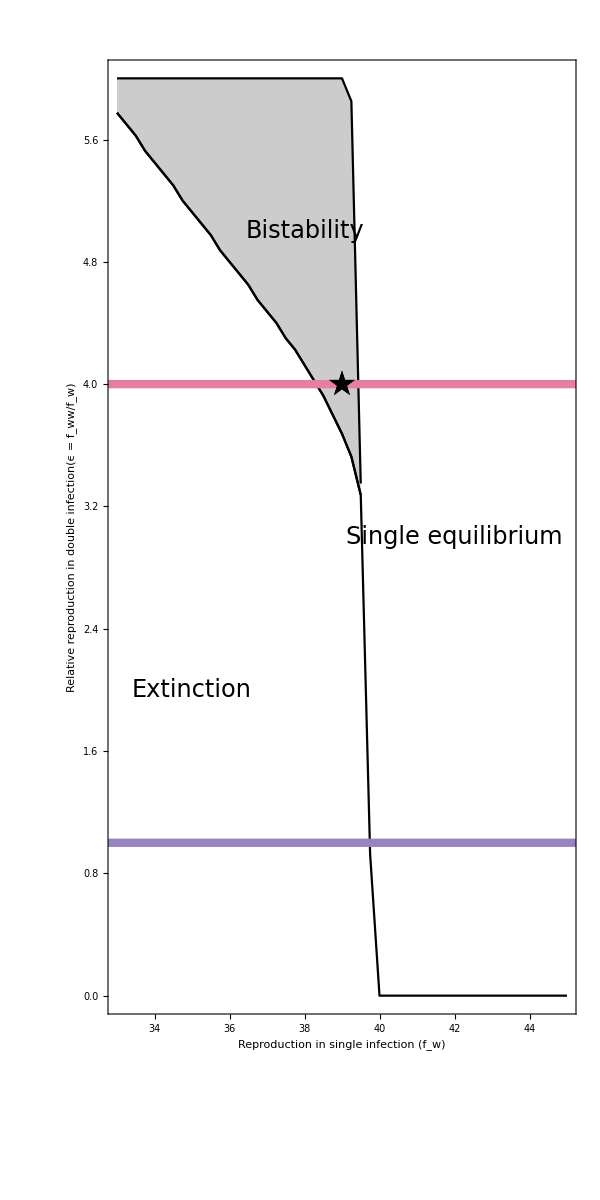

reproduction_bifurcationA.pdf

```mathematica
eqϵfw =eq/. Flatten[ϵfwAllresults, 2];
ϵfwlist = ϵfw/.Flatten[ϵfwAllresults, 2];
(*rangeϵfw= {{ϵstart , ϵend}, {fwstart , fwend}};*)
rangeϵfw= { {fwstart , fwend}, {ϵstart , ϵend}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parϵfw,{ϵ, fw}, ϵfwlist, eqϵfw, colorstable, True];
MakeListPlotData[ϵfwlist[[All, 1]], ϵfwlist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->rangeϵfw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, GridLines->{{1},{}}, GridLinesStyle-> Directive[Thick,
Red], LabelStyle->labelStyle,FrameStyle->frameStyle,AspectRatio->1];
GetBoundaryLineBiStable[ϵfwlist];
p1 =ListLinePlot[%, PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Reproduction in single infection (f_w)", "Relative reproduction in double infection(ϵ = f_ww/f_w)"}, LabelStyle->labelStyle,GridLines->{{},{{1, col2}, {4, col1}}},GridLinesStyle->Thickness[0.01], PlotStyle-> Black, Filling-> {1-> {2}}];
GetBoundaryLineSingle[ϵfwlist];
p2 = ListLinePlot[%,  PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, PlotStyle-> Black];
ip = ip = ListLinePlot[{{39, 4}}, PlotRange->rangeϵfw, PlotMarkers -> {"★", 28},Frame->includeFrame, FrameStyle->frameStyle, PlotStyle-> Black, ImageSize->imageSize, LabelStyle->labelStyle];
GraphicsGrid[{{p0, Show[{p1, p2}]}}];
pϵfw = Show[{p1, p2, ip}, ImageSize-> {imageSize , imageSize * 2},Epilog->{ Text[Style["Extinction", FontSize->24], {35, 2}],
			Text[Style["Single equilibrium", FontSize->24], {42, 3}], Text[Style["Bistability", FontSize->24], {38, 5.}]}, AspectRatio-> 2/1, LabelStyle->labelStyle, ImagePadding->{{90(*left*),5(*right*)},{65(*bottom*),10(*top*)}}]
Export["reproduction_bifurcationA.pdf", %, ImageResolution-> figResolution]
```

## Combined bifurcation plot

```mathematica
GraphicsGrid[{{pϵfw, pIw}, {SpanFromAbove, ppIw}}, Spacings->{0, 0}, Frame->All, ImageSize-> 1600];
(*Export["reproduction_bifurcation.pdf", %, ImageResolution-> figResolution]*)
```

## Bifurcation of single and double infection (β_w and β_ww) setting f_ww=ϵ f_w

```mathematica
βwstart = 0;
βwend = 4;
βwstep = 0.15;
βwwstart = 0;
βwwend =4;
βwwstep = 0.15;
range= {{βwstart, βwend}, {βwwstart, βwwend}};
```

## Parameter set 1 (f_ww=3.5 f_w)

CALCULATE

```mathematica
parmanip1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4.5, fw -> 37, h-> 0.6};
		    
manipAllResults1 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip1, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 3.670934174584352. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

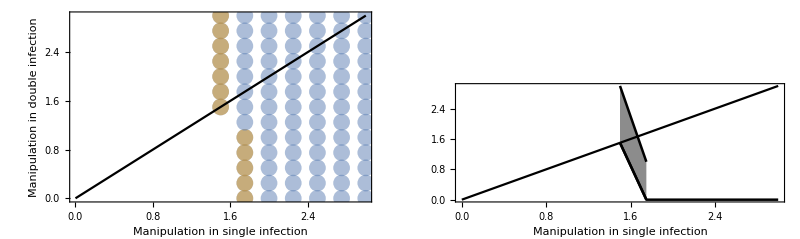

```mathematica
equilibrium =eq/. Flatten[manipAllResults1 , 2];
parslist = β/.Flatten[manipAllResults1, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle, ImageSize->imageSize];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black, ImageSize->imageSize];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle, PlotStyle->  {{Thickness[thick], colbifur[[1]]},{Thickness[thick], colbifur[[1]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[1]],ImageSize->imageSize, Epilog-> {Text[Style["Extinction", FontSize->20], {0.4, 4}], Text[Style["Single equilibrium", FontSize->20], {1.5, 9}]}];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[1]]}, ImageSize->imageSize];
l21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l21}}]
```

## Contour Plot for Reproduction ratio

### Reproduction ratio

```mathematica
βwstart = 0;
βwend = 4;
βwstep =0.15(* 0.05;*)
βwwstart = 0;
βwwend =4;
βwwstep = 0.15(*0.05;*)
range= {{βwstart, βwend}, {βwwstart, βwwend}};
parmanipR0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4.5, fw -> 37, h-> 0.6};
		    
manipAllResultsR0 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipR0, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

0.15

0.15

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 3.670934174584352. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

### Plot

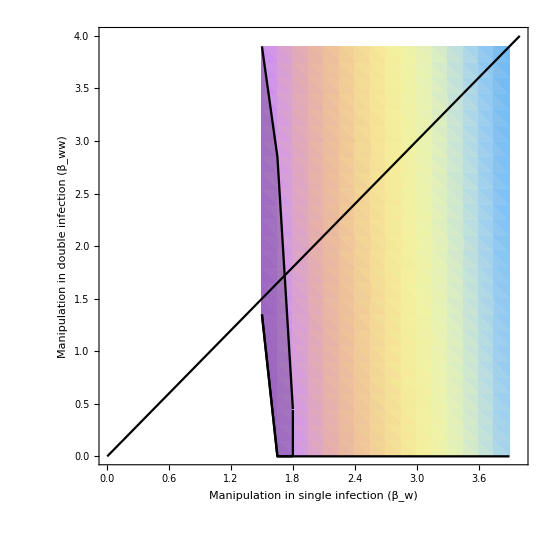

manip_bifur_R0.pdf

```mathematica
thickR0 = 0.003;
equilibrium =eq/. Flatten[manipAllResultsR0 , 2];
parslist = β/.Flatten[manipAllResultsR0, 2];
R0numeric = R0func1/.{Iw -> 0, Iww->0, Dw-> 0, Dww->0 , W-> 0}/.diseasefree/.fww-> ϵ fw/.parmanipR0/. Thread[{Thread[βw->parslist[[All, 1]]],Thread[βww-> parslist[[All, 2]]]}];

zrange={Min[R0numeric], Max[R0numeric]};
barleg=BarLegend[{coldat, zrange}, {1, 1.1, 1.2, 1.3, 1.4}, LegendMarkerSize->320, LegendLayout->"Row"];
(* Plot R0*)
Join[parslist, Partition[R0numeric, 1], 2];
R0g = ListDensityPlot[%,  Frame-> includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Manipulation in single infection (β_w)", "Manipulation in double infection (β_ww)"}, ImageSize->imageSize, ColorFunction->coldat,PlotLegends->Placed[barleg, {Above,Right}](*, ColorFunctionScaling->False*),PlotRange->range, ImagePadding->{{60,5},{65,30}}];
(* Plot Subscript[β, w] = Subscript[β, ww] line*)
p0 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black, ImageSize->imageSize];

(* Plot bistability area*)
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipR0,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
bnd1 = GetBoundaryLineBiStable[parslist];
p1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection (β_w)", "Manipulation in double infection (β_ww)"}, LabelStyle->labelStyle, PlotStyle->  {{Thickness[thickR0], Black},{Thickness[thickR0],Black}}, Filling-> {{1-> {2}}},FillingStyle->Directive[Black,HatchFilling[Pi, 2, 6]] ,ImageSize->imageSize];
bnd2 = GetBoundaryLineSingle[parslist];
p2= ListLinePlot[Join[{%, {{1.55, 4.6}, {1.55, 6}}, {{1.8, 0}, {1.8, 0.44}}}],  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> { {Thickness[thickR0], Black},{Thickness[thickR0],  Black}}];
p3 = Show[{p1,p2, p0}];

R0gfinal = Show[{  R0g, p3}, ImageSize-> 550]
Export[ "manip_bifur_R0.pdf", %, ImageResolution-> figResolution]
```

## Parameter set 2 (f_ww = 4 f_w)

CALCULATE

```mathematica
parmanip2 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4., fw -> 40, h-> 0.6};
manipAllResults2 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip2, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -13.5751039991322. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

{{0,5},{0,5}}

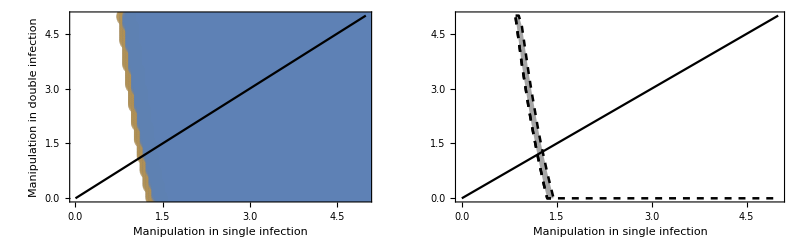

```mathematica
range
equilibrium =eq/. Flatten[manipAllResults2 , 2];
parslist = β/.Flatten[manipAllResults2, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip2,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""},  LabelStyle->labelStyle,PlotStyle-> {{Thickness[thick], colbifur[[2]], Dashed}, {Thickness[thick], colbifur[[2]], Dashed}}, Filling-> {1-> {2}},FillingStyle->colbifurfilling[[2]], ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2 = ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dashed,Thickness[thick], colbifur[[2]]}];
l22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l22}}]
```

## Parameter set 3 (f_ww = 4.5 f_w)

CALCULATE

```mathematica
parmanip3 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4.5, fw -> 40, h-> 0.6};
manipAllResults3 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip3, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.357628204577584. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -13.33675969089882. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

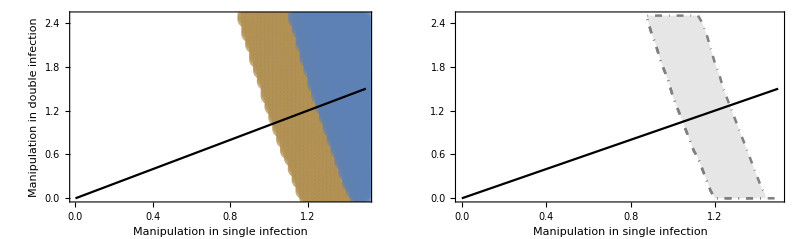

```mathematica
equilibrium =eq/. Flatten[manipAllResults3 , 2];
parslist = β/.Flatten[manipAllResults3, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip3,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""},LabelStyle->labelStyle, PlotStyle->{ {DotDashed, Thickness[thick], colbifur[[3]]}, {DotDashed, Thickness[thick], colbifur[[3]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[3]], ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2 = ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed, Thickness[thick], colbifur[[3]]}];
l23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l23}}]
```

## Combined plots

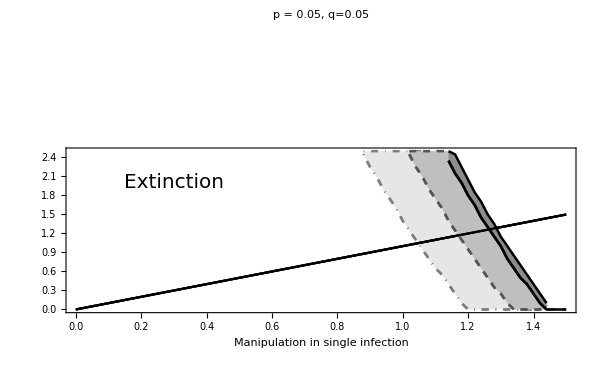

```mathematica
customizeLegend = SwatchLegend[colbifurfilling,{"f_ww = 3.5 f_w","f_ww = 4 f_w","f_ww = 4.5 f_w"}, LegendMarkers->{Graphics[{EdgeForm[{Thickness[0.05], Black, Opacity[1]}],Rectangle[]}],Graphics[{EdgeForm[{Dashed, Black, Thickness[0.1], Opacity[0.5]}],Rectangle[]}], Graphics[{EdgeForm[{DotDashed, Black, Thickness[0.1], Opacity[0.3]}],Rectangle[]}]}, LabelStyle->{FontSize-> 14}, LegendMarkerSize->20];
cbp1 = Show[{l23,l22,l21},PlotLabel->"p = 0.05, q=0.05",
	 Epilog->{ Inset[
	Framed[
		customizeLegend
		] ,
	{0.2, 6.7}
				],
			Text[Style["Extinction", FontSize->20], {0.3, 2}],
			 Text[Style["Single equilibrium", FontSize->20], {1.25, 5}]}]
```

## Bifurcation of single and double infection (β_w and β_ww) with higher coinfection from parasite pool to intermediate host

```mathematica
βwstart = 0;
βwend = 1.5;
βwstep = 0.02;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;
```

## Parameter set 1 (f_ww= 3.5 f_w)

CALCULATION

```mathematica
parmanipHcoin1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.2, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 3.5, fw -> 40, h-> 0.6};
manipHcoinAllResults1 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin1, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 4.119577623268038. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

$Aborted

PLOT

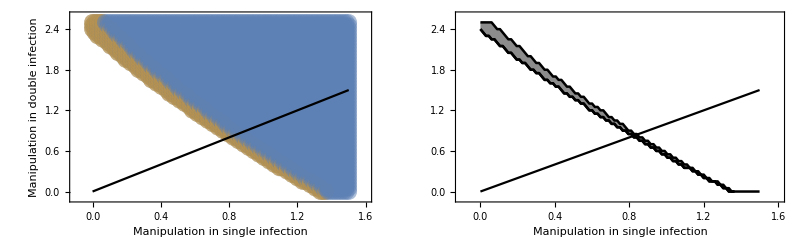

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults1 , 2];
parslist = β/.Flatten[manipHcoinAllResults1, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle,PlotStyle->  {{Thickness[thick], colbifur[[1]]},{Thickness[thick], colbifur[[1]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[1]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle->  {{Thickness[thick], colbifur[[1]]},{Thickness[thick], colbifur[[1]]}}];
lHC21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC21}}]
```

## Parameter set 2 (f_ww = 2 f_w)

CALCULATION

```mathematica
parmanipHcoin2= {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.2, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4, fw -> 40, h-> 0.6};
manipHcoinAllResults2 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin2, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859281622852025. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859304638616045. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859360916591762. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859313232958273. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

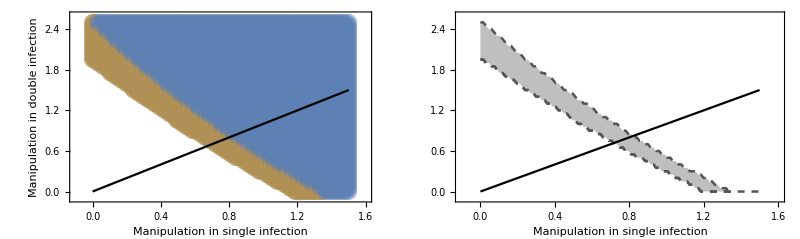

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults2 , 2];
parslist = β/.Flatten[manipHcoinAllResults2, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin2,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle, PlotStyle-> {{Dashed,Thickness[thick], colbifur[[2]]}, {Dashed,Thickness[thick], colbifur[[2]]}}, Filling-> {1-> {2}},  FillingStyle-> colbifurfilling[[2]],ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dashed, Thickness[thick], colbifur[[2]]}];
lHC22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC22}}]
```

## Parameter set 3 (f_ww = 4.5 f_w)

```mathematica
parmanipHcoin3= {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.2, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4.5, fw -> 40, h-> 0.6};
manipHcoinAllResults3 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin3, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.8593525116260808. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 4.6279711434541836. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 4.62791866074220686. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -9.266974319992344+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859416744576918. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859400335044992. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859283519742762. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.85936514142155. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

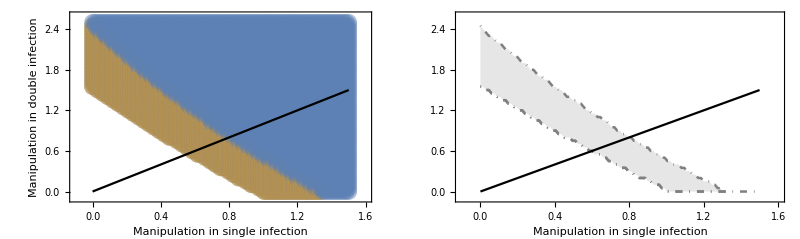

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults3, 2];
parslist = β/.Flatten[manipHcoinAllResults3, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin3,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp3 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{ "Manipulation in single infection", ""},  LabelStyle->labelStyle,PlotStyle-> {{DotDashed,Thickness[thick], colbifur[[3]]}, {DotDashed,Thickness[thick], colbifur[[3]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[3]], ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colbifur[[3]]}];
lHC23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp3, lHC23}}]
```

## Combined plot

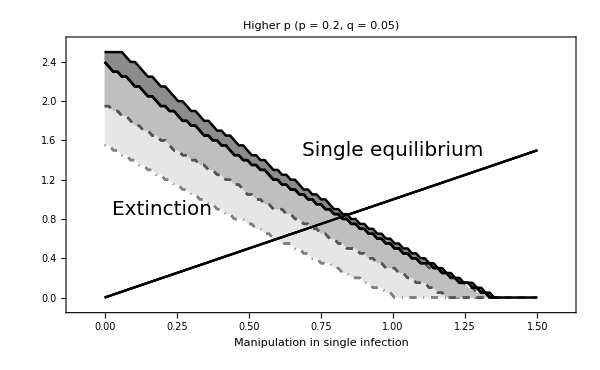

```mathematica
cbp2 = Show[{lHC23, lHC22, lHC21 },PlotLabel-> "Higher p (p = 0.2, q = 0.05)",
	 Epilog->{ Text[Style["Extinction", FontSize->20], {0.2, 0.9}],
			Text[Style["Single equilibrium", FontSize->20], {1., 1.5}]}]
```

## Manipulation bifurcation graph when coinfection from intermediate to definitive host is high

```mathematica
βwstart = 0;
βwend = 1.5;
βwstep = 0.02;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;
```

## Parameter set 1 (f_ww= 3.5 f_w)

CALCULATE

```mathematica
parmanipHcoin4 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.2, δ-> 0.9, k -> 0.26, ϵ-> 3.5, fw -> 40, h-> 0.6};
manipHcoinAllResults4 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin4, {βw -> x}, {βww-> y}, β, eq,varRes, 12],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -133.86033189743271+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

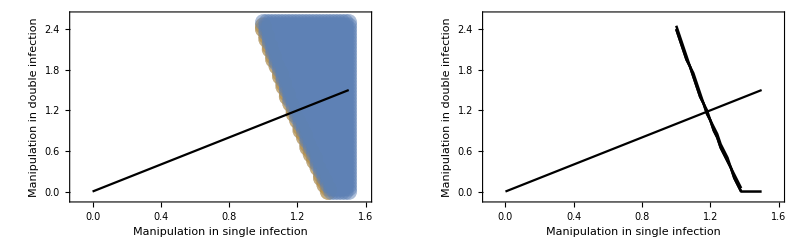

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults4 , 2];
parslist = β/.Flatten[manipHcoinAllResults4, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin4,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle->  {{Thickness[thick], colbifur[[1]]},{Thickness[thick], colbifur[[1]]}}, Filling-> {1-> {2}}, FillingStyle->{colbifurfilling[[1]]},LabelStyle->labelStyle, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle->  {{Thickness[thick], colbifur[[1]]},{Thickness[thick], colbifur[[1]]}}];
lHCq21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHCq21}}]
```

## Parameter set 2 (fww = 2 fw)

CALCULATE

```mathematica
parmanipHcoin5 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.2, δ-> 0.9, k -> 0.26, ϵ-> 4, fw -> 40, h-> 0.6};
manipHcoinAllResults5 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin5, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859460749000961. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859433741960719. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.85929558961605. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

General::stop: Further output of NSolve::sfail will be suppressed during this calculation.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859373908934352. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

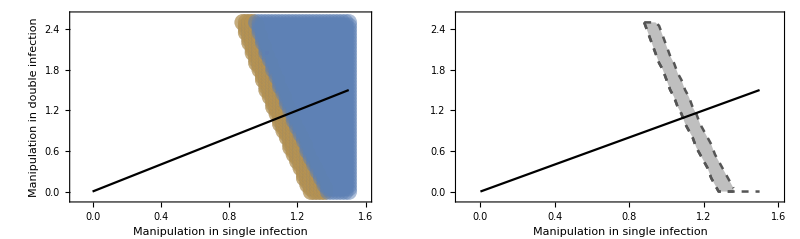

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults5 , 2];
parslist = β/.Flatten[manipHcoinAllResults5, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin5,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle, PlotStyle-> {{Dashed,Thickness[thick], colbifur[[2]]}, {Dashed,Thickness[thick], colbifur[[2]]}}, Filling-> {1-> {2}}, FillingStyle->{colbifurfilling[[2]]},ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dashed,Thickness[thick], colbifur[[2]]}];
lHCq22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHCq22}}]
```

## Parameter set 3 (fww = 0.5 fw)

CALCULATE

```mathematica
parmanipHcoin6 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.2, δ-> 0.9, k -> 0.26, ϵ-> 4.5, fw -> 40, h-> 0.6};

manipHcoinAllResults6 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin6, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.3572648455316673. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859269853445835. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -6.778165951698758+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

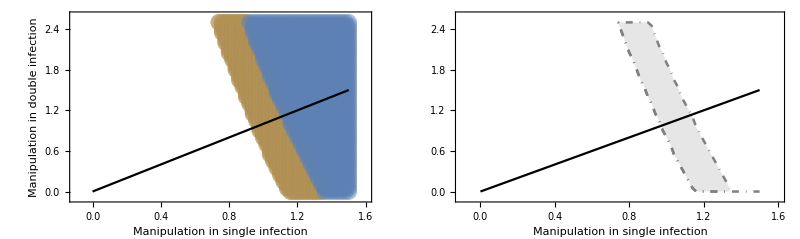

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults6, 2];
parslist = β/.Flatten[manipHcoinAllResults6, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin6,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp3 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle,PlotStyle-> {{DotDashed, Thickness[thick],colbifur[[3]]}, {DotDashed, Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {2}},FillingStyle->{colbifurfilling[[3]]},  ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colbifur[[3]]}];
lHCq23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp3, lHCq23}}]
```

## Combined plot

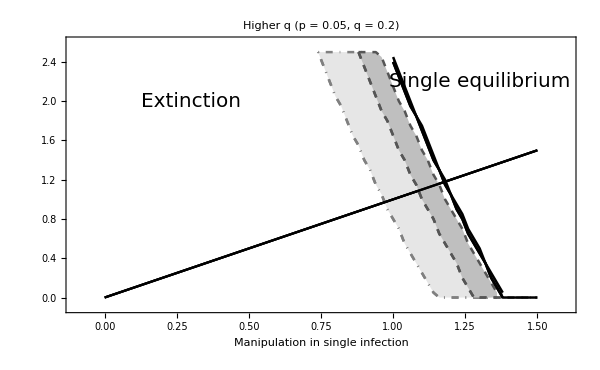

```mathematica
cbp3 = Show[{lHCq23, lHCq22, lHCq21 },PlotLabel-> "Higher q (p = 0.05, q = 0.2)",
	 Epilog->{ Text[Style["Extinction", FontSize->20], {0.3, 2.}],
			Text[Style["Single equilibrium", FontSize->20], {1.3, 2.2}], Arrow[{{1,18},{1.5,18}}]}]
```

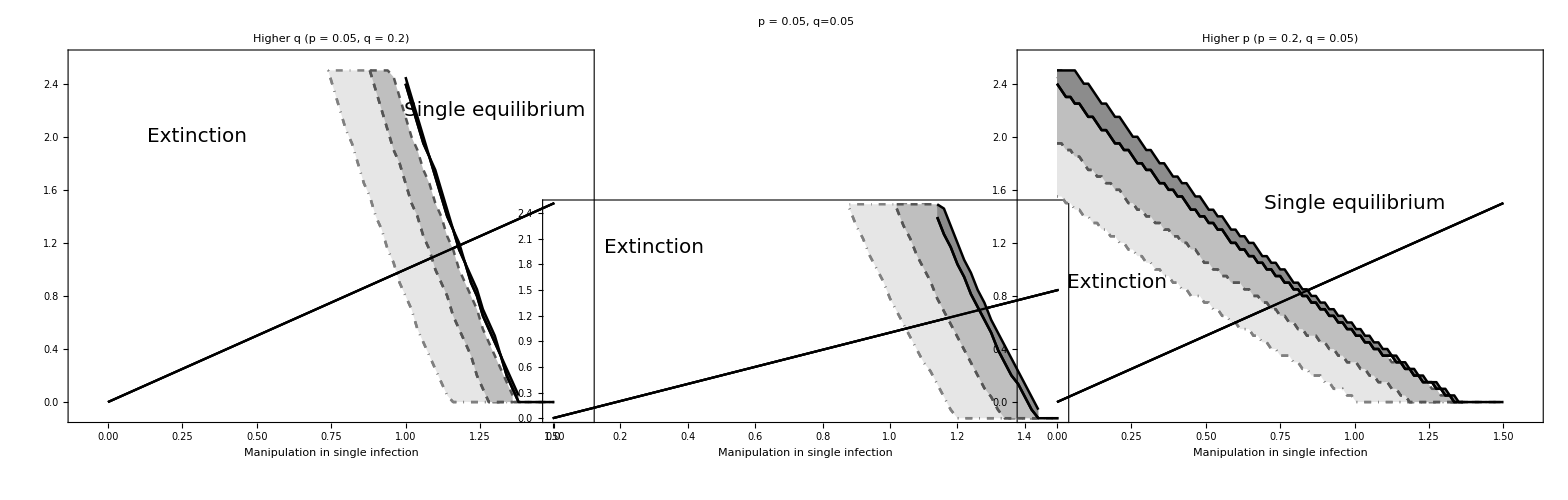

```mathematica
Size = {1700, 500};
GraphicsRow[{ cbp3,cbp1, cbp2}, ImageSize->Size, Spacings->-140]
(*Export["manip_bifurcation.pdf",%, ImageResolution-> figResolution]*)
```

## Manipulation ratio representation

```mathematica
βwwstart = 0.1;
βwwend = 3;
βwwstep =0.03;
ϵstart = 0.5;
ϵend = 12;
ϵstep = 0.2;
alpha = 0.6;
```

### Changing reproduction in single infection

### fw = 37, βw = 1.65

CALCULATION

```mathematica
parmanipβϵ ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 37, h-> 0.6, βw-> 1.65};
manipβϵAllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
range1= {{βwwstart/(βw/.parmanipβϵ),βwwend/(βw/.parmanipβϵ) }, {ϵstart, ϵend + 0.1}}
```

{{0.0606061,1.81818},{0.5,12.1}}

PLOT

```mathematica
equilibrium =eq/. Flatten[manipβϵAllResults, 2];
parslist = βϵ/.Flatten[manipβϵAllResults, 2];

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ), parslist[[All, 2]]];
pβϵ = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβϵ1 =ListLinePlot[%,  PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle,PlotStyle-> {{Thick, Thickness[thick],colbifur[[3]]}, {Thick, Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {{2}, Directive[Opacity[alpha],colbifurfilling[[3]]]}},  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thick,Thickness[thick], colbifur[[3]]},FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", "Relative reproduction \n in double infections(f_ww/f_w)"}, Filling->Bottom, FillingStyle->Directive[LightGray,HatchFilling[]]];
lβϵ = Show[{lpβϵ2,lpβϵ1}];
GraphicsGrid[{{pβϵ, lβϵ}}]
```

-Graphics-

### fw = 38, βw = 1.65

```mathematica
parmanipβϵ1 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.65};
manipβϵ1AllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ1, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

```mathematica
equilibrium =eq/. Flatten[manipβϵ1AllResults, 2];
parslist = βϵ/.Flatten[manipβϵ1AllResults, 2];


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ1,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ1), parslist[[All, 2]]];
pβϵ1= ListPlot[%,  PlotStyle->marklist, PlotRange->range1, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ1, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ1, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβϵ1 =ListLinePlot[%,  PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", " \n "},PlotStyle-> {{Thick, Thickness[thick],colbifur[[3]]}, {Thick, Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {{2}, Directive[Opacity[alpha], colbifurfilling[[3]]]}},  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ1, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thick,Thickness[thick], colbifur[[3]]}, Filling->Bottom, FillingStyle->Directive[LightGray,HatchFilling[]]];
lβϵ1 = Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ1, lβϵ1}}]
```

-Graphics-

### fw = 37, βw = 1.60

```mathematica
parmanipβϵ2 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 37., h-> 0.6, βw-> 1.60};
manipβϵ2AllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ2, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
range2= {{βwwstart/(βw/.parmanipβϵ2),βwwend/(βw/.parmanipβϵ2) }, {ϵstart, ϵend + 0.1}};
```

```mathematica
equilibrium =eq/. Flatten[manipβϵ2AllResults, 2];
parslist = βϵ/.Flatten[manipβϵ2AllResults, 2];


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ2,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ2), parslist[[All, 2]]];
pβϵ2= ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ2, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ2, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβϵ1 =ListLinePlot[%,  PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", " Relative reproduction \n in double infections(f_ww/f_w) "},PlotStyle-> {{Thickness[thick],colbifur[[3]]}, {Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {2}},FillingStyle->Directive[Opacity[alpha], colbifurfilling[[3]]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ2, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[3]]}, Filling->Bottom, FillingStyle->Directive[LightGray, HatchFilling[]]];
lβϵ2 = Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ2, lβϵ2}}]
```

-Graphics-

-Graphics-

### fw = 38, βw = 1.60

```mathematica
parmanipβϵ3 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.60};
manipβϵ3AllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ3, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

```mathematica
equilibrium =eq/. Flatten[manipβϵ3AllResults, 2];
parslist = βϵ/.Flatten[manipβϵ3AllResults, 2];


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ3,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ3), parslist[[All, 2]]];
pβϵ3= ListPlot[%,  PlotStyle->marklist, PlotRange->range2, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ3, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ3, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβϵ1 =ListLinePlot[%,  PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", " \n "},PlotStyle-> {{Thickness[thick],colbifur[[3]]}, {Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {2}},FillingStyle->Directive[Opacity[alpha], colbifurfilling[[3]]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ3, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[3]]}, Filling->Bottom, FillingStyle->Directive[LightGray,HatchFilling[]]];
lβϵ3 = Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ3, lβϵ3}}]
```

-Graphics-

### Combined graph

```mathematica
legBox = {Graphics[{EdgeForm[{Thickness[0.1], Black, Opacity[1]}],Rectangle[]}],
	      Graphics[{EdgeForm[{Thickness[0.1],Black, Dashed, Opacity[0.7]}],Rectangle[]}], 
	      Graphics[{EdgeForm[{Thickness[0.1], Black, DotDashed, Opacity[0.3]}],Rectangle[]}](*,
	      Graphics[{EdgeForm[{Thickness[0.1], Black, Dotted, Opacity[0.1]}],Rectangle[]}]*)};
line = {Graphics[{Thickness[0.005],Black,Line[{{1, range[[2]][[1]]}, {1, 12.5}}]}], Graphics[{Thickness[0.005],Black,Line[{{range[[1]][[1]], 1}, {2.25, 1}}]}]};
arrowsize = {-0.02,0.02}
arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range1[[1]][[1]], 12.4}}], Text[Style["Sabotage", FontSize->22], {0.5, 12.9}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range1[[1]][[2]], 12.4}}], Text[Style["Cooperation", FontSize->22], {1.4, 12.9}]} ];
arrow3 = Graphics[{Arrowheads[arrowsize],Arrow[{{1.9, 1}, {1.9, range1[[2]][[2]]}}], Rotate[Text[Style["Enhancement", FontSize->22], {1.96, 6.7}], -90 Degree]} ];
arrow4 = Graphics[{Text[Style["Suppression", FontSize->22], {2.01, 0.55}]} ];
customizeLegend = SwatchLegend[colbifurfilling,{"f_w = 38","f_w = 37.5", "f_w = 37"}, LegendMarkers->legBox, LabelStyle->{FontSize-> 20}(*, LegendMarkerSize->20*)];
plotlβϵfull1 = Show[{ lβϵ, line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{150, 200}, {100, 45}},
	 Epilog->{ (*Inset[Framed[customizeLegend],{2.1, 10.4}],*)Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.6, 9.5}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationA.pdf", %, ImageResolution-> figResolution]
plotlβϵfull1 = Show[{ lβϵ1,line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 200}, {100, 45}},
	 Epilog->{ (*Inset[Framed[customizeLegend],{2.1, 10.4}],*)Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.6, 9.5}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationB.pdf", %, ImageResolution-> figResolution]

arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range2[[1]][[1]], 12.4}}], Text[Style["Sabotage", FontSize->22], {0.5, 12.9}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range2[[1]][[2]], 12.4}}], Text[Style["Cooperation", FontSize->22], {1.4, 12.9}]} ];
arrow3 = Graphics[{Arrowheads[arrowsize],Arrow[{{1.96, 1}, {1.96, range2[[2]][[2]]}}], Rotate[Text[Style["Enhancement", FontSize->22], {2.02, 6.7}], -90 Degree]} ];
arrow4 = Graphics[{Text[Style["Suppression", FontSize->22], {2.07, 0.55}]} ];
plotlβϵfull1 = Show[{ lβϵ2,line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{150, 200}, {100, 45}},
	 Epilog->{ (*Inset[Framed[customizeLegend],{2.1, 10.4}],*)Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.7, 11.2}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationC.pdf", %, ImageResolution-> figResolution]
plotlβϵfull1 = Show[{ lβϵ3,line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 200}, {100, 45}},
	 Epilog->{ (*Inset[Framed[customizeLegend],{2.1, 10.4}],*)Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.6, 9.5}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationD.pdf", %, ImageResolution-> figResolution]
```

{-0.02,0.02}

-Graphics-

ratio_reproduction_manipulationA.pdf

-Graphics-

ratio_reproduction_manipulationB.pdf

-Graphics-

ratio_reproduction_manipulationC.pdf

-Graphics-

ratio_reproduction_manipulationD.pdf

## Changing p

```mathematica
βwwstart = 0.1;
βwwend = 6.8;
βwwstep = 0.05(*0.1;*)
coldat="Rainbow";
```

0.05

CALCULATION

```mathematica
parmanipβp ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.4, ϵ -> 4.5};
manipβpAllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβp, {βww-> x}, {p-> y}, βp, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, 0, 1,0.007(* 0.007*)}];
```

PLOT

```mathematica
equilibrium =eq/. Flatten[manipβpAllResults, 2];
parslist = βp/.Flatten[manipβpAllResults, 2];
range= {{βwwstart/(βw/.parmanipβp),βwwend/(βw/.parmanipβp) }, {0, 1}};
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβp,{βww, p}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβp), parslist[[All, 2]]];
pβp = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "p"}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβp, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβp, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infection (β_ww/β_w)", "Cotransmission (p) \n parasite pool - intermediate host"},PlotStyle-> {{ Thickness[thick],Black}, {Thickness[thick],Black}}, Filling-> {1-> {2}},FillingStyle->colbifur[[3]],  ImageSize->imageSize,PlotLabel->Pane["A)", Alignment->Left, ImageSize->panellabel], InterpolationOrder->intorder];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβp, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], Black}, InterpolationOrder->intorder];
line = {Graphics[{Thickness[0.005],Black,Line[{{1, 0}, {1, 1.1}}]}]};
arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, { βwwstart/(βw/.parmanipβp),1.02}}], Text[Style["Sabotage", FontSize->20], {0.5, 1.08}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, {βwwend/(βw/.parmanipβp), 1.02}}], Text[Style["Cooperation", FontSize->20], {2.9, 1.08}]} ];
lβp = Show[{ lpβp1,lpβp2, line, arrow1, arrow2},Epilog->{Text[Style["Extinction", FontSize->20], {0.5, 0.07}],Text[Style["Single \n equilibrium", FontSize->20], {3.3, 0.6}]},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 20}, {100, 45}}, ImageSize-> imageSize/1.5];
GraphicsGrid[{{pβp, lβp}}];
```

## Changing q

CALCULATION

```mathematica
parmanipβq ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.45, ϵ -> 4.5};
manipβqAllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβq, {βww-> x}, {q-> y}, βq, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, 0, 1, 0.007(*0.007*)}];
```

PLOT

{-0.02,0.02}

Join::headsd: Expression Idensity at position 2 is expected to have head List for all expressions at level 2.

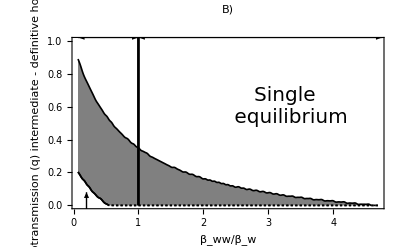

```mathematica
equilibrium =eq/. Flatten[manipβqAllResults, 2];
parslist = βq/.Flatten[manipβqAllResults, 2];
range= {{βwwstart/(βw/.parmanipβq),βwwend/(βw/.parmanipβq) }, {0, 1}};
arrowsize = {-0.02,0.02}

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβq,{βww, q}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβq), parslist[[All, 2]]];
pβq = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "q"}, LabelStyle->labelStyle];
Join[Thread@{parslist[[All, 1]]/(βw/.parmanipβq), parslist[[All, 2]]},Idensity, 2];
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβq, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβq, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβq1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"β_ww/β_w", "Cotransmission (q) \n intermediate - definitive host"},PlotStyle-> {{Thickness[thick],Black}, {Thickness[thick],Black}}, Filling-> {1-> {2}},FillingStyle->Gray,  ImageSize->imageSize, PlotLabel->Pane["B)", Alignment->Left, ImageSize->panellabel], InterpolationOrder->intorder];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβq, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβq2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick],Black}, InterpolationOrder->intorder];
line = {Graphics[{Thickness[0.005],Black,Line[{{1, 0}, {1, 1.1}}]}]};
arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, { βwwstart/(βw/.parmanipβp),1.02}}], Text[Style["Sabotage", FontSize->20], {0.5, 1.08}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, {βwwend/(βw/.parmanipβp)-0.1, 1.02}}], Text[Style["Cooperation", FontSize->20], {2.9, 1.08}]} ];
arrow3 = Graphics[{Arrow[{{0.2, -0.06}, {0.2, 0.08}}]}];
lβq = Show[{lpβq1,lpβq2, line, arrow1, arrow2, arrow3}, Epilog-> {Text[Style["Extinction", FontSize->20], {0.2, -0.09}],Text[Style["Single \n equilibrium", FontSize->20], {3.3, 0.6}]},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 20}, {110, 45}}, ImageSize-> imageSize/1.5]
(*GraphicsGrid[{{pβq, lβq}}]*)
```

## Combined graph

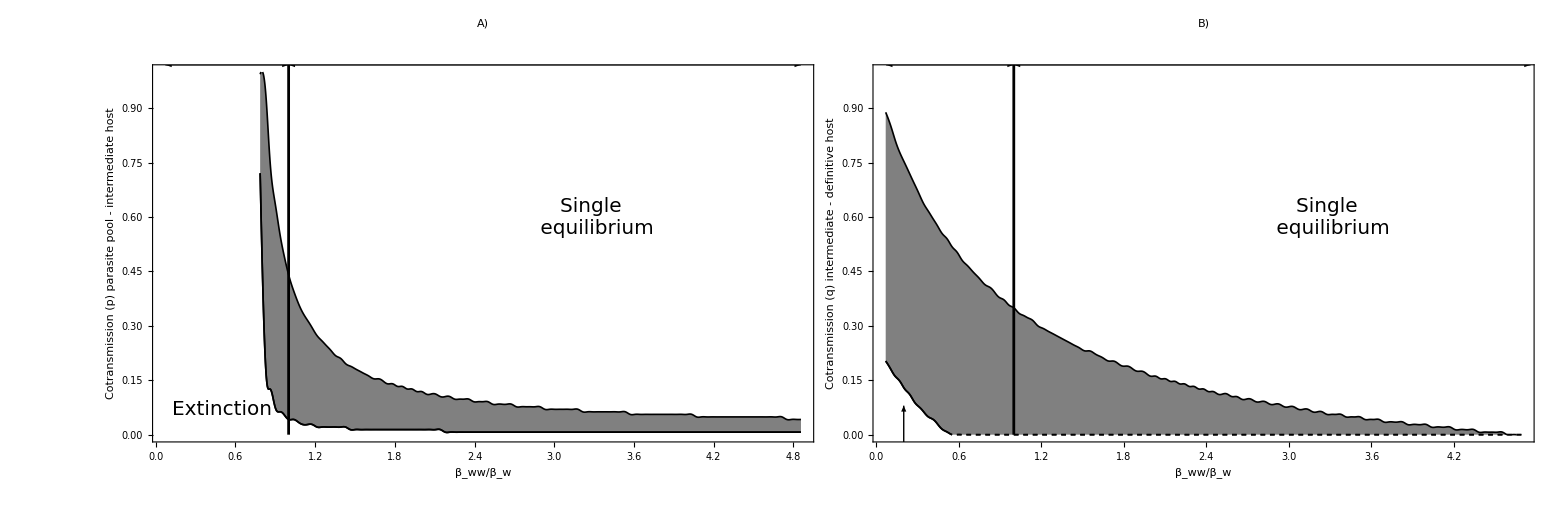

coinfect_transmission.pdf

```mathematica
GraphicsGrid[{{lβp, lβq}},ImageSize->imageSize*2.8, Spacings-> -60]
Export["coinfect_transmission.pdf", %, ImageResolution-> figResolution]
```

## Changing manipulation in single infection

### βw = 1.90

```mathematica
βwwstart = 1.90* range[[1]][[1]];
βwwend = 1.90 * range[[1]][[2]];
βwwstep =0.1; 
parmanipβϵ4 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 35, h-> 0.6, βw-> 1.90};
manipβϵAllResults4 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ4, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 12],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.357671904801231066. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.691406048143359564. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

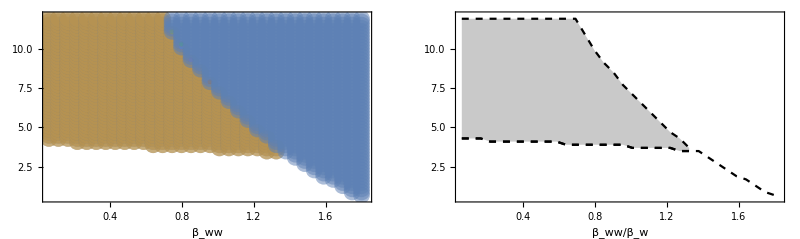

```mathematica
equilibrium =eq/. Flatten[manipβϵAllResults4, 2];
parslist = βϵ/.Flatten[manipβϵAllResults4, 2];


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ4,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ4), parslist[[All, 2]]];
pβϵ4= ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww", ""}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ4, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ4, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβϵ1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"β_ww/β_w", ""},PlotStyle-> {{Dashed,colbifur[[2]]}, {Dashed,colbifur[[2]]}}, Filling-> {1-> {2}},FillingStyle->Directive[Opacity[alpha], colbifurfilling[[2]]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ4, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dashed, colbifur[[2]]}];
lβϵ4= Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ4, lβϵ4}}]
```

### βw = 1.95

```mathematica
βwwstart =1.95 * range[[1]][[1]];
βwwend = 1.95 * range[[1]][[2]];
βwwstep =0.1; 
parmanipβϵ5={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 35, h-> 0.6, βw-> 1.95};
manipβϵAllResults5 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ5, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 12],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.35716068749732603. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 6.057241886380252. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.357631046836224866. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

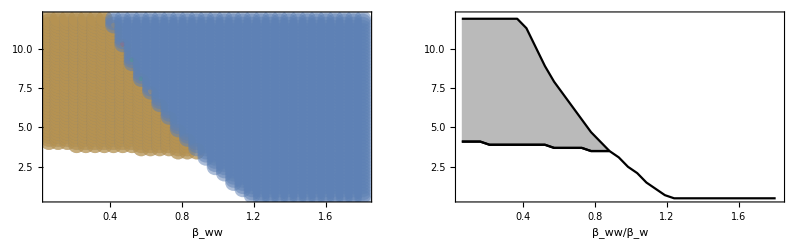

```mathematica
equilibrium =eq/. Flatten[manipβϵAllResults5, 2];
parslist = βϵ/.Flatten[manipβϵAllResults5, 2];


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ5,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ5), parslist[[All, 2]]];
pβϵ5= ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww", ""}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ5, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ5, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβϵ1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"β_ww/β_w", ""},PlotStyle-> {{colbifur[[1]]}, {colbifur[[1]]}}, Filling-> {1-> {2}},FillingStyle->Directive[Opacity[alpha], colbifurfilling[[1]]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ5, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {colbifur[[1]]}];
lβϵ5 = Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ5, lβϵ5}}]
```

### βw = 1.85

```mathematica
βwwstart = 1.85 * range[[1]][[1]];
βwwend = 1.85 * range[[1]][[2]];
βwwstep =0.05; 
parmanipβϵ6={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 35, h-> 0.6, βw-> 1.85};
manipβϵAllResults6 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ6, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 12],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 4.534351534534976. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.357372116314762003. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 4.952530823476656049. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 4.77615174273339326. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

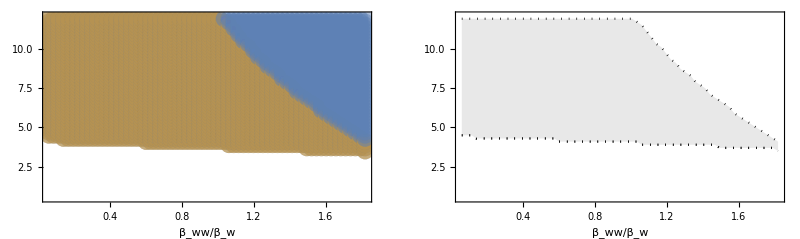

```mathematica
equilibrium =eq/. Flatten[manipβϵAllResults6, 2];
parslist = βϵ/.Flatten[manipβϵAllResults6, 2];

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ6,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ6), parslist[[All, 2]]];
pβϵ6= ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", ""}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ6, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ6, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβϵ1 =ListLinePlot[%,PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"β_ww/β_w", ""},PlotStyle-> {{Dotted,colbifur[[4]]}, {Dotted,colbifur[[4]]}}, Filling-> {1-> {2}},FillingStyle->Directive[Opacity[alpha], colbifurfilling[[4]]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ6, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dotted, colbifur[[4]]}];
lβϵ6= Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ6, lβϵ6}}]
```

{-0.02,0.02}

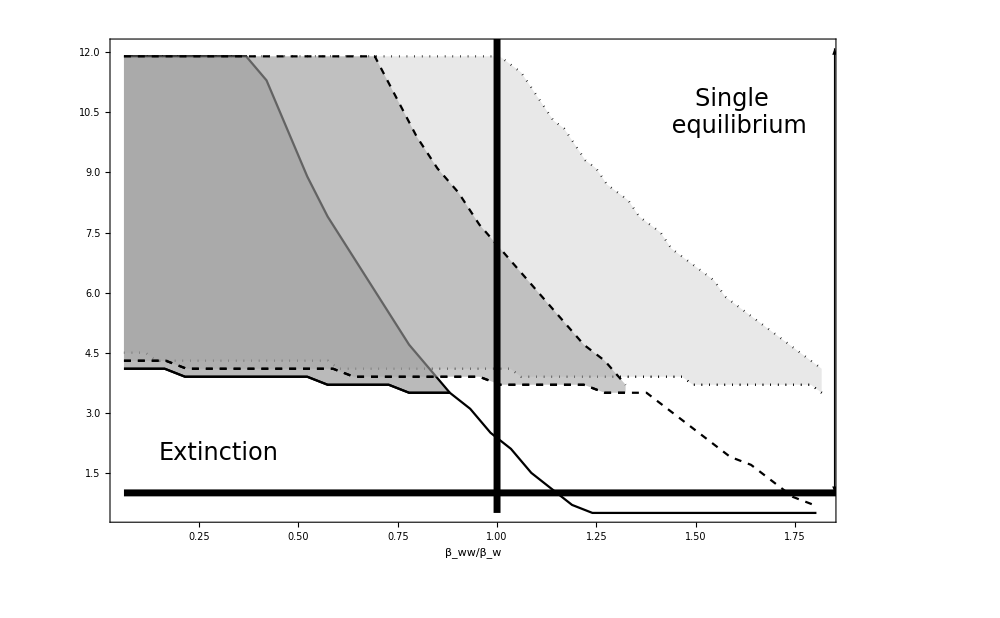

ratio_reproduction_manipulation_beta.pdf

```mathematica
legBox = {Graphics[{EdgeForm[{Thickness[0.1], Black, Opacity[1]}],Rectangle[]}],
	      Graphics[{EdgeForm[{Thickness[0.1],Black, Dashed, Opacity[0.7]}],Rectangle[]}], 
	      Graphics[{EdgeForm[{Thickness[0.1], Black, DotDashed, Opacity[0.3]}],Rectangle[]}],
	      Graphics[{EdgeForm[{Thickness[0.1], Black, Dotted, Opacity[0.1]}],Rectangle[]}]};
line = {Graphics[{Thickness[0.005],Black,Line[{{1, range[[2]][[1]]}, {1, 12.5}}]}], Graphics[{Thickness[0.005],Black,Line[{{range[[1]][[1]], 1}, {2.25, 1}}]}]};
arrowsize = {-0.02,0.02}
arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.6}, {range[[1]][[1]], 12.6}}], Text[Style["Sabotage", FontSize->22], {0.5, 12.9}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.6}, {range[[1]][[2]], 12.6}}], Text[Style["Cooperation", FontSize->22], {1.4, 12.9}]} ];
arrow3 = Graphics[{Arrowheads[arrowsize],Arrow[{{1.85, 1}, {1.85, range[[2]][[2]]}}], Rotate[Text[Style["Enhancement", FontSize->22], {1.9, 6.5}], -90 Degree]} ];
arrow4 = Graphics[{Text[Style["Suppression", FontSize->22], {2.05, 0.7}]} ];
customizeLegend = SwatchLegend[colbifurfilling,{"β_w = 1.95","β_w = 1.90","β_w = 1.85"}, LegendMarkers->legBox, LabelStyle->{FontSize-> 20}, LegendMarkerSize->20];
plotlβϵfull2 = Show[{  lβϵ6,lβϵ5,lβϵ4,line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{100, 200}, {100, 45}},PlotRange-> range,
	 Epilog->{ Inset[Framed[customizeLegend],{2.05, 10.5}],Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.6, 10.5}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulation_beta.pdf", %, ImageResolution-> figResolution]
```